I start off every notebook with these two commands to clear the namespace and anchor the directory

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
```

The file we need is on Census.gov

```mathematica
censusURI = "https://www2.census.gov/topics/genealogy/2010surnames/names.zip";
files = Import[censusURI, "ZIP"]
```

{Names_2010Census.csv,Names_2010Census.xlsx}

```mathematica
names = Import[censusURI, First@files];
```

```mathematica
names[[1;;5]]
```

{{name,rank,count,prop100k,cum_prop100k,pctwhite,pctblack,pctapi,pctaian,pct2prace,pcthispanic},{SMITH,1,2442977,828.19,828.19,70.9,23.11,0.5,0.89,2.19,2.4},{JOHNSON,2,1932812,655.24,1483.42,58.97,34.63,0.54,0.94,2.56,2.36},{WILLIAMS,3,1625252,550.97,2034.39,45.75,47.68,0.46,0.82,2.81,2.49},{BROWN,4,1437026,487.16,2521.56,57.95,35.6,0.51,0.87,2.55,2.52}}

```mathematica
header = { "surname", "rank", "count", "per_100K" };
data = #[[1;;4]]& /@ Rest@names;
data[[1;;5]]
```

{{SMITH,1,2442977,828.19},{JOHNSON,2,1932812,655.24},{WILLIAMS,3,1625252,550.97},{BROWN,4,1437026,487.16},{JONES,5,1425470,483.24}}

```mathematica
population = Total[#[[3]]& /@ data]
```

294979229

Looks like we want to exclude the final row

```mathematica
Last@data
```

{ALL OTHER NAMES,0,29312001,9936.97}

Percent of people with names with N < 100

```mathematica
100. * data[[-1,3]] / population
```

9.93697

```mathematica
surnames = AssociationThread[header, #]& /@ data[[1;;-2]];
surnames[[1;;5]]
```

{<|surname→SMITH,rank→1,count→2442977,per_100K→828.19|>,<|surname→JOHNSON,rank→2,count→1932812,per_100K→655.24|>,<|surname→WILLIAMS,rank→3,count→1625252,per_100K→550.97|>,<|surname→BROWN,rank→4,count→1437026,per_100K→487.16|>,<|surname→JONES,rank→5,count→1425470,per_100K→483.24|>}

```mathematica
firstLetters = Append[#, "first" -> StringTake[#["surname"], 1]]& /@ surnames;
firstLetters[[1;;5]]
```

{<|surname→SMITH,rank→1,count→2442977,per_100K→828.19,first→S|>,<|surname→JOHNSON,rank→2,count→1932812,per_100K→655.24,first→J|>,<|surname→WILLIAMS,rank→3,count→1625252,per_100K→550.97,first→W|>,<|surname→BROWN,rank→4,count→1437026,per_100K→487.16,first→B|>,<|surname→JONES,rank→5,count→1425470,per_100K→483.24,first→J|>}

```mathematica
byFirst = GroupBy[firstLetters, #["first"]&];
byFirst[["A"]][[1;;5]]
```

{<|surname→ANDERSON,rank→15,count→784404,per_100K→265.92,first→A|>,<|surname→ALLEN,rank→33,count→482607,per_100K→163.61,first→A|>,<|surname→ADAMS,rank→42,count→427865,per_100K→145.05,first→A|>,<|surname→ALVAREZ,rank→92,count→233983,per_100K→79.32,first→A|>,<|surname→ALEXANDER,rank→118,count→204621,per_100K→69.37,first→A|>}

```mathematica
totalByLetter[letter_] := Total[#["count"]& /@ byFirst[letter]];
totalByLetter["W"]
```

14741478

```mathematica
frequencies = AssociationThread[Keys@byFirst, totalByLetter[#]& /@ Keys@byFirst]
```

<|S→25056728,J→7935401,W→14741478,B→22587641,G→14814448,M→25610240,D→12045696,R→15699799,H→18810320,L→13045257,A→10080086,T→9413187,P→13233868,C→20582563,Y→1684921,K→8669408,N→5069517,F→8981809,E→4932313,O→4051850,V→4657504,Z→1504404,Q→642349,I→1097235,U→617005,X→102201|>

```mathematica
namesList = SortBy[Transpose[{Keys@frequencies, Values@frequencies}], First]
```

{{A,10080086},{B,22587641},{C,20582563},{D,12045696},{E,4932313},{F,8981809},{G,14814448},{H,18810320},{I,1097235},{J,7935401},{K,8669408},{L,13045257},{M,25610240},{N,5069517},{O,4051850},{P,13233868},{Q,642349},{R,15699799},{S,25056728},{T,9413187},{U,617005},{V,4657504},{W,14741478},{X,102201},{Y,1684921},{Z,1504404}}

When in doubt, visualize!

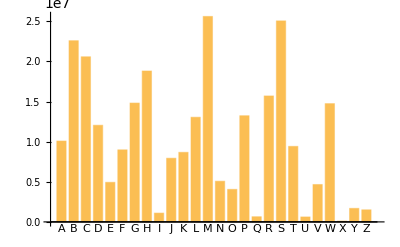

```mathematica
BarChart[Last /@ namesList, ChartLabels -> First /@ namesList]
```

```mathematica
total = Total[Last /@ namesList]
```

265667228

```mathematica
letters = Keys@frequencies
```

{S,J,W,B,G,M,D,R,H,L,A,T,P,C,Y,K,N,F,E,O,V,Z,Q,I,U,X}

```mathematica
percents = Reverse@Sort[frequencies / total * 1.0];
```

Okay, how do we divide into groups?

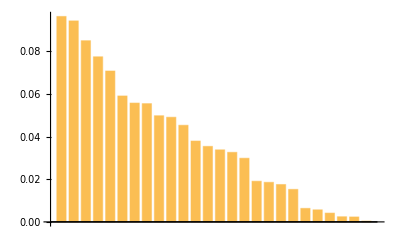

```mathematica
BarChart[percents]
```

Let’s try assigning pairs from the first 24

```mathematica
percentsInverse = AssociationThread[Values@percents, Keys@percents]
```

<|0.0963997→M,0.0943162→S,0.0850223→B,0.077475→C,0.0708041→H,0.0590957→R,0.0557632→G,0.0554885→W,0.0498137→P,0.0491037→L,0.0453413→D,0.0379425→A,0.0354322→T,0.0338085→F,0.0326326→K,0.0298697→J,0.0190822→N,0.0185658→E,0.0175313→V,0.0152516→O,0.00634222→Y,0.00566274→Z,0.00413011→I,0.00241787→Q,0.00232247→U,0.000384696→X|>

Let’s start with the n largest values

```mathematica
values = Values@percents;
n = 4;
groups = List /@ values[[1;;n]]
remaining = values[[n + 1;;]]
```

{{0.0963997},{0.0943162},{0.0850223},{0.077475}}

{0.0708041,0.0590957,0.0557632,0.0554885,0.0498137,0.0491037,0.0453413,0.0379425,0.0354322,0.0338085,0.0326326,0.0298697,0.0190822,0.0185658,0.0175313,0.0152516,0.00634222,0.00566274,0.00413011,0.00241787,0.00232247,0.000384696}

Now we’ll iteratively add to the smallest group to make it the largest by the smallest margin

```mathematica
addOneEqualize[groups_, remaining_] := (
	sorted = Reverse@SortBy[groups, Total@#&];
	totals = Total /@ sorted;
	diff = First@totals - Last@totals;
	smallestGreater = Last@Select[remaining, # > diff&];
	If[Length@smallestGreater == 0,
		smallestGreater = Last@remaining;
	];	
	next = Append[Most@sorted, Append[Last@sorted, smallestGreater]];
	index = First@First@Position[remaining, smallestGreater];
	stillStanding = Delete[remaining, index];
	{ next, stillStanding }
)
```

And quantify the results

```mathematica
measure[groupCandidate_] := (
	totals = Total /@ groups;
	lengths = Length /@ groups;
	<|
		"spread" -> Max@totals - Min@totals,
		"largestGroup" -> Max@lengths,
		"smallestGroup" -> Min@lengths
	|>
)
```

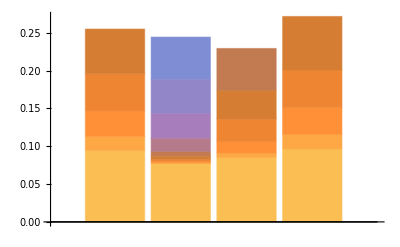

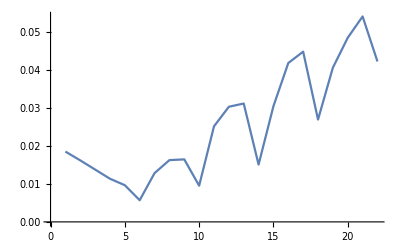

<|spread→0.0422945,largestGroup→10,smallestGroup→5|>

```mathematica
measuresEqualized = {};
While[Length@remaining > 0, 
	(
		{ groups, remaining } = addOneEqualize[groups, remaining];
		measuresEqualized = Append[measuresEqualized, measure[groups]["spread"]];
	)
]
equalizedGroups = groups;

BarChart[
	equalizedGroups,
	ChartLayout->"Stacked"
]
ListLinePlot[measuresEqualized]
measure[equalizedGroups]
```

Those results aren’t bad, but not necessarily perfect. We’d prefer either a lower spread or more equally sized groups

```mathematica
values = Values@percents;
n = 4;
groups = List /@ values[[1;;n]];
remaining = values[[n + 1;;]];
```

```mathematica
addOneLargest[groups_, remaining_] := (
	sorted = Reverse@SortBy[groups, Total@#&];
	totals = Total /@ sorted;
	nextGreatest = First@remaining;
	next = Append[Most@sorted, Append[Last@sorted, nextGreatest]];
	index = First@First@Position[remaining, nextGreatest];
	stillStanding = Delete[remaining, index];
	{ next, stillStanding }
)
```

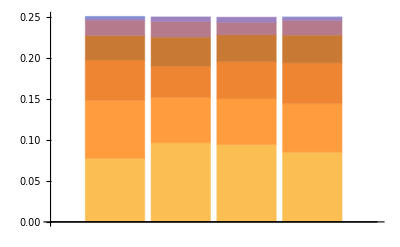

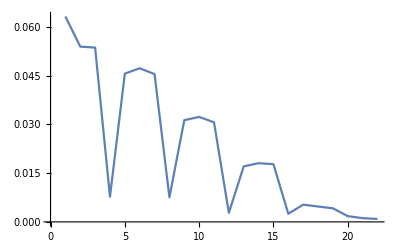

<|spread→0.000911505,largestGroup→7,smallestGroup→6|>

```mathematica
measuresLargest = {};
While[Length@remaining > 0, 
	(
		{ groups, remaining } = addOneLargest[groups, remaining];
		measuresLargest = Append[measuresLargest, measure[groups]["spread"]];
	)
]
largestGroups = groups;

BarChart[
	largestGroups,
	ChartLayout->"Stacked"
]
ListLinePlot[measuresLargest]
measure[largestGroups]
```

MUCH better! Let’s reverse to the letters

```mathematica
valuesToLetters[subgroup_] := percentsInverse[#]& /@ subgroup
```

```mathematica
groupsByLetter = valuesToLetters /@ largestGroups
```

{{C,H,L,J,E,Q,U},{M,W,A,T,N,Z},{S,G,D,K,O,Y},{B,R,P,F,V,I,X}}

```mathematica
newAlphabet = Flatten@groupsByLetter
```

{C,H,L,J,E,Q,U,M,W,A,T,N,Z,S,G,D,K,O,Y,B,R,P,F,V,I,X}

Let' s see what a frequency group looks like

```mathematica
colors = { RGBColor["#ffe229"], RGBColor["#d91400"], RGBColor["#006206"], RGBColor["#ab025e"] }
```

{RGBColor[1., 0.8862745098039215, 0.1607843137254902],RGBColor[0.8509803921568627, 0.0784313725490196, 0.],RGBColor[0., 0.3843137254901961, 0.023529411764705882],RGBColor[0.6705882352941176, 0.00784313725490196, 0.3686274509803922]}

```mathematica
getColor[letter_] := colors[[First@Flatten@Position[MemberQ[#, letter]& /@ groupsByLetter, True]]]
```

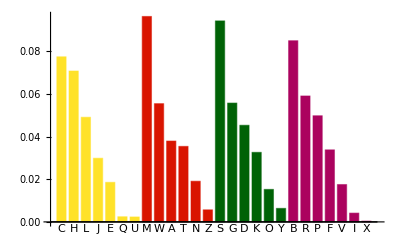

```mathematica
BarChart[
	Flatten[largestGroups],
	ChartLabels->newAlphabet,
	ColorFunctionScaling->False,
	ColorFunction->Function[v, getColor[percentsInverse[v]]]
]
```

Let’s make signs

```mathematica
sequences = StringRiffle[#, ","]& /@ groupsByLetter
```

{C,H,L,J,E,Q,U,M,W,A,T,N,Z,S,G,D,K,O,Y,B,R,P,F,V,I,X}

```mathematica
makePlacard[sequence_] := Framed[Column[
	{
		Column[Style[#, 14, Darker@Gray]& /@ {"Please queue here for", "last names beginning with" }, Center],
		Style[sequence, 36]
	}, Center, Spacings->1], FrameMargins->{{20,20},{20,16}}, RoundingRadius->5, ImageSize->400, Alignment->Center]
Column[makePlacard /@ sequences, Center]
```

Please queue here for
last names beginning with
C,H,L,J,E,Q,U
Please queue here for
last names beginning with
M,W,A,T,N,Z
Please queue here for
last names beginning with
S,G,D,K,O,Y
Please queue here for
last names beginning with
B,R,P,F,V,I,X